Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

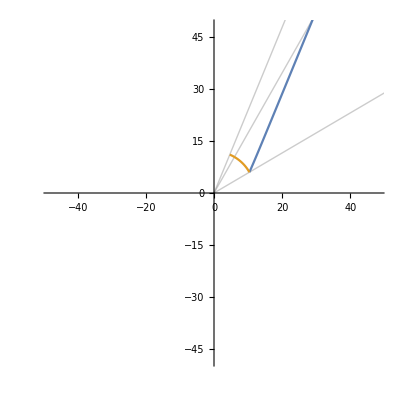

upperLimit: 11387.7

π/6 < θ < 1.17372

Time elapsed: 1.037178

Ax = 0.998385, Ay = 0., φ = 0.00161537

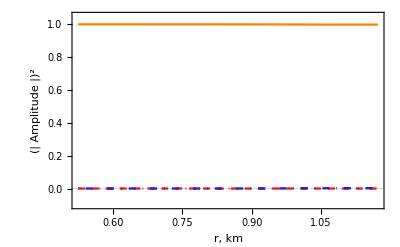

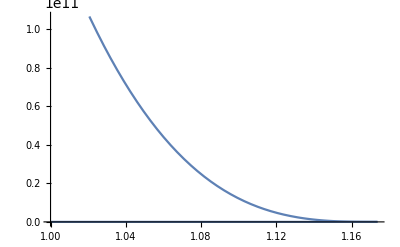

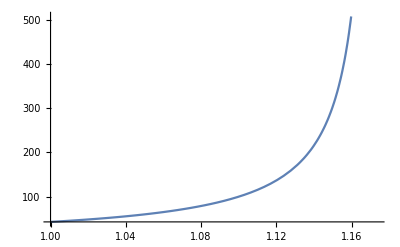

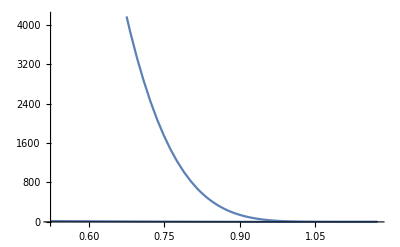

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

upperLimit: 11387.7

π/6 < θ < 1.17372

Time elapsed: 1.07528

Ax = 0.998385, Ay = 0., φ = 0.00161537

-Graphics-

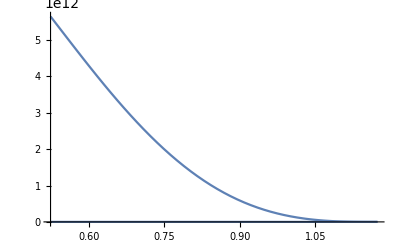

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;

(*θ:=Pi/3;*)
angleChi:=0Pi/6;
angleGamma:=0;

bR:=fDip*BSurf*(R0/trajectoryR)^3*(Sin[angleChi]*Sin[θ]*Cos[angleGamma]+Cos[angleChi]*Cos[θ]);
bTheta:=gDip*0.5*BSurf*(R0/trajectoryR)^3*(-Sin[angleChi]*Cos[θ]*Cos[angleGamma]+Cos[angleChi]*Sin[θ]);
bPhi:=gDip*0.5*BSurf*(R0/trajectoryR)^3*(Sin[angleChi]*Sin[angleGamma]);


(*Ray bending*)
trajectoryR=Sqrt[rg^2(1-Cos[θ-angleInclination-angleEmissionPoint])^2/(4(1+Cos[θ-angleInclination-angleEmissionPoint])^2)+bImp^2/Sin[θ-angleInclination-angleEmissionPoint]^2]-rg(1-Cos[θ-angleInclination-angleEmissionPoint])/(2(1+Cos[θ-angleInclination-angleEmissionPoint]));

bImp:=R0 Sin[angleEmissionDirectionAlpha]/Sqrt[1-rg/R0];

angleEmissionDirectionAlpha:=Pi/6;
rg:=4.134;
angleEmissionPoint:=Pi/6;

angleInclination=t/.Solve[1-Cos[angleEmissionDirectionAlpha]==(1-Cos[t])(1-rg/R0),t][[2]];

p1=PolarPlot[{trajectoryR,R0},{θ,angleEmissionPoint,angleEmissionPoint+angleInclination}, PlotRange->4R0,PolarGridLines->{{angleEmissionPoint+angleInclination,angleEmissionDirectionAlpha+angleEmissionPoint,angleEmissionPoint},{}}]








fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/trajectoryR;

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.θ->angleEmissionPoint;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.θ->angleEmissionPoint;

bRep:={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;



k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);


(*Параметры АЛП*)
ω0=1;
g=6*10^(-20);
m=10^(-8);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/trajectoryR))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaCEDxx:=k0 delta M/2;
deltaCEDyy:=k0 delta n/2;
deltaCEDxy:=k0 delta P/2;
deltaCEDyx:=deltaCEDxy;

(*Матрица М*)
mat:={{  deltaCEDxx,deltaCEDxy,deltaMx    },
	{deltaCEDyx,deltaCEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[θ_]:={{r11[θ],r12[θ],r13[θ]},{r21[θ],r22[θ],r23[θ]},{r31[θ],r32[θ],r33[θ]}};

(*Список начальных условий*)
(*O-mode*)
rmat0={{r11[angleEmissionPoint]==1,r12[angleEmissionPoint]==0,r13[angleEmissionPoint]==0},{r21[angleEmissionPoint]==0,r22[angleEmissionPoint]==0,r23[angleEmissionPoint]==0},{r31[angleEmissionPoint]==0,r32[angleEmissionPoint]==0,r33[angleEmissionPoint]==0}};
(*X-mode*)
(*rmat0={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};*)

upperLimitSolve=angleEmissionPoint+0.999angleInclination;
upperLimitPlot=angleEmissionPoint+0.999angleInclination;

Print["upperLimit: ",trajectoryR/.θ->angleEmissionPoint+0.999angleInclination];
Print[angleEmissionPoint," < θ < ",angleEmissionPoint+0.999angleInclination];

eqs=NDSolve[Join[{ⅈ rmat'[θ]==rmat[θ].mat-mat.rmat[θ]/.bRep},rmat0],{r11[θ],r22[θ],r33[θ]},{θ,angleEmissionPoint,upperLimitSolve}];
(*eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];*)


(*Print[mat/.bRep/.z->100//MatrixForm];*)

Print["Time elapsed: ",AbsoluteTime[]-time];

(*Print["Fields at z = 100: ",(bx/Sqrt[by^2+bx^2])/.bRep/.z->100];*)

Print["Ax = ",Re[r11[θ]]/.eqs[[1]]/.θ->upperLimitSolve,", Ay = ",Re[r22[θ]]/.eqs[[1]]/.θ->upperLimitSolve,", φ = ",Re[r33[θ]]/.eqs[[1]]/.θ->upperLimitSolve];

p1=Plot[Re[Evaluate[{r11[θ]}/.eqs]],{θ,angleEmissionPoint,upperLimitPlot},PlotRange->{{angleEmissionPoint,upperLimitPlot},{-0.1,1.05}},PlotTheme->"Scientific",PlotStyle->Orange, PlotLegends->Placed[LineLegend[{Directive[Orange]},{Superscript["|A_x|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14}],{0.92,0.8}]];

p2=Plot[Re[Evaluate[{r22[θ]}/.eqs]],{θ,angleEmissionPoint,upperLimitPlot},PlotRange->{{angleEmissionPoint,upperLimitPlot},{-0.1,1.05}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed}, PlotLegends->Placed[LineLegend[{Directive[Red,Dashed]},{Superscript["|A_y|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14}],{0.92,0.8}]];

p3=Plot[Re[Evaluate[{r33[θ]}/.eqs]],{θ,angleEmissionPoint,upperLimitPlot},PlotRange->{{angleEmissionPoint,upperLimitPlot},{-0.1,1.05}},PlotTheme->"Scientific",PlotStyle->{Blue,DotDashed}, PlotLegends->Placed[LineLegend[{Directive[Blue,DotDashed]},{Superscript["|φ|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14}],{0.92,0.8}]];

(*Show[p1,p2,p3]*)
Show[p1,p2,p3,FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["r, km",16],Style[Superscript[" | Amplitude | " ,2],16]}]

p4=Plot[{bx,by}/.bRep,{θ,1,upperLimitPlot}]
p4=Plot[{trajectoryR}/.bRep,{θ,1,upperLimitPlot}]
p5=Plot[{deltaMx,deltaCEDxx}/.bRep,{θ,angleEmissionPoint,upperLimitPlot}]
```

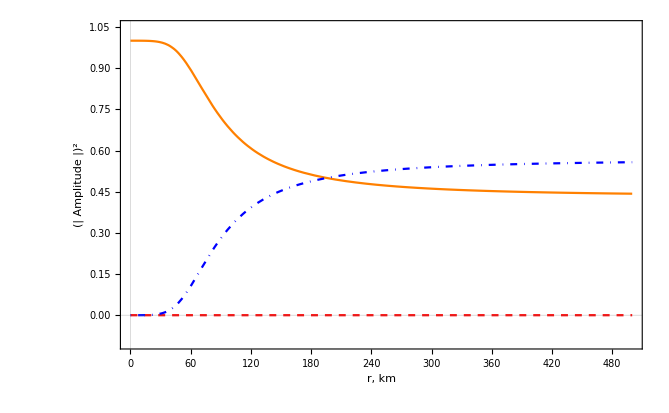

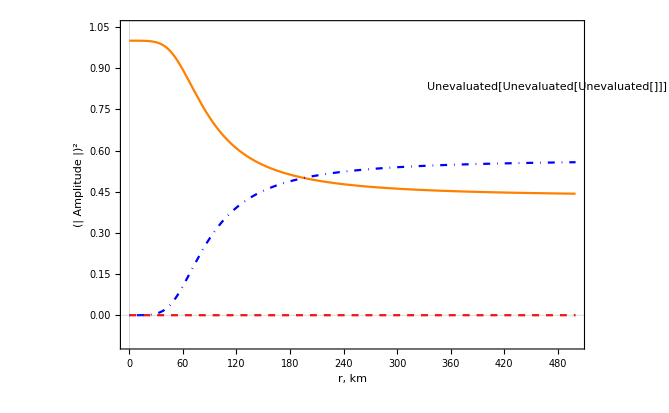

```mathematica
(*Проверка условий смешивания*)

For[dist:=1.,dist<10000,dist+=dist/3,
(*If[
((Abs[deltaCEDxx-deltaMass]<5Abs[deltaMx]||Abs[deltaCEDyy-deltaMass]<5Abs[deltaMy])&&(2Pi/Sqrt[(deltaCEDxx-deltaMass)^2+4deltaMx^2]<10dist||2Pi/Sqrt[(deltaCEDyy-deltaMass)^2+deltaMy^2]<dist))/.bRep/. z->dist,
Print[dist," < r < ",dist+dist],
Print[-1]
]*)

(*Print[dist," < r < ",dist+dist/3," : ",Abs[deltaCEDxx-deltaMass]<5Abs[deltaMx]||Abs[deltaCEDyy-deltaMass]<Abs[deltaMy]/.bRep/. z->dist]*)
Print[dist," < r < ",dist+dist/3," : ",2Pi/Sqrt[(deltaCEDxx-deltaMass)^2+4deltaMx^2]<5/3dist||2Pi/Sqrt[(deltaCEDyy-deltaMass)^2+4deltaMy^2]<dist/.bRep/. z->dist]
]
```

1. < r < 1.33333 : True

1.33333 < r < 1.77778 : True

1.77778 < r < 2.37037 : True

2.37037 < r < 3.16049 : True

3.16049 < r < 4.21399 : True

4.21399 < r < 5.61866 : True

5.61866 < r < 7.49154 : True

7.49154 < r < 9.98872 : True

9.98872 < r < 13.3183 : True

13.3183 < r < 17.7577 : True

17.7577 < r < 23.677 : True

23.677 < r < 31.5693 : True

31.5693 < r < 42.0924 : True

42.0924 < r < 56.1232 : True

56.1232 < r < 74.8309 : True

74.8309 < r < 99.7746 : True

99.7746 < r < 133.033 : False

133.033 < r < 177.377 : False

177.377 < r < 236.503 : False

236.503 < r < 315.337 : False

315.337 < r < 420.449 : False

420.449 < r < 560.599 : False

560.599 < r < 747.465 : False

747.465 < r < 996.62 : False

996.62 < r < 1328.83 : False

1328.83 < r < 1771.77 : False

1771.77 < r < 2362.36 : False

2362.36 < r < 3149.81 : False

3149.81 < r < 4199.75 : False

4199.75 < r < 5599.67 : False

5599.67 < r < 7466.22 : False

7466.22 < r < 9954.96 : False

9954.96 < r < 13273.3 : False

```mathematica
BSurf:=1.5*10^13;
R0:=12;
angleTheta:=Pi/3;
angleChi:=Pi/6;
angleGamma:=0;

bR:=BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Cos[angleTheta]);
bTheta:=0.5*BSurf*(R0/(2z+R0))^3*(-Sin[angleChi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Sin[angleTheta]);
bPhi:=-0.5*BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleGamma]);

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;
Print["angleRotation: ",angleRotation];

bX:=bTheta*sinRotation+bPhi*cosRotation;
bY:=bTheta*cosRotation-bPhi*sinRotation;

Print["bTheta: ",bTheta/.z->0];
Print["bPhi: ",bPhi/.z->0];
Print["bX: ",bX/.z->0];
Print["bY: ",bY/.z->0];
```

angleRotation: angleRotation

bTheta: 3.75×10^12

bPhi: 0.

bX: 3.75×10^12

bY: 0.

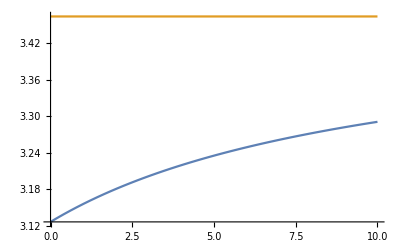

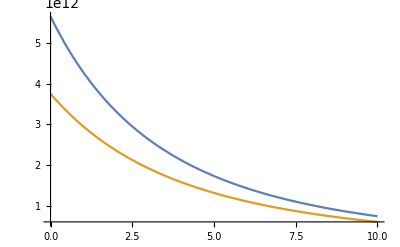

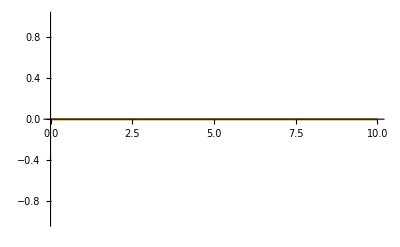

```mathematica
bR:=fDip*BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Cos[angleTheta]);
bTheta:=gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleChi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Sin[angleTheta]);
bPhi:=gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleGamma]);

bRdip:=BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Cos[angleTheta]);
bThetadip:=0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleChi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleChi]*Sin[angleTheta]);
bPhidip:=0.5*BSurf*(R0/(z+R0))^3*(Sin[angleChi]*Sin[angleGamma]);

p4=Plot[{bR/bTheta,bRdip/bThetadip},{z,0,10}]
p5=Plot[{bTheta,bThetadip},{z,0,10}]
p5=Plot[{bPhi,bPhidip},{z,0,10}]
```